## First we generate all graphs

We will generate an association containing all graphs.  The key of the graph is computed based on a base 4 representation of the upper half of the “adjacency matrix”.
The matrix itself is tri-valued since 0 means no edge, 1 means and edge and 2 mean they are the same vertex.
For each graph we keep

signature  : the "key"
matrix : the "adjancency matrix"
vertexsets : the "sets " of vertices where contracted vertices are in the same set
vertices : th evertices of the graph
edges : the edges of the graph
graph : a picture of the graph

```mathematica
baseGraphs6=GenAll[6];Length[baseGraphs6]
```

53071

## Now we calculate the relations

We calculate the relations between the graphs.  This is based on the deletion contraction rule.  It links 6 graphs together in a a=b+c relation (or a subtraction)

```mathematica
withRelations6=CompleteRelations[baseGraphs6];Length[withRelations6]
```

53071

For each graph we now add

links  : ids of graphs that are  linked to this graph
relations : a set of equations that involve the current graph.  This set can be empty.  The graph can be mentioned in the relations section of another graph

## Impose a colofour value for the 15 base graphs and propagate this to the others

```mathematica
Table[Labeled[withRelations6[k,"graph"],k],{k,Take[Keys[withRelations6],20]}]
```

{-Graphics-0,-Graphics-1,-Graphics-2,-Graphics-3,-Graphics-4,-Graphics-6,-Graphics-9,-Graphics-10,-Graphics-12,-Graphics-13,-Graphics-14,-Graphics-16,-Graphics-18,-Graphics-22,-Graphics-26,-Graphics-27,-Graphics-28,-Graphics-30,-Graphics-31,-Graphics-36}

We take a list of graphs as defined in https://en.wikipedia.org/wiki/Bell_number and give them an arbitrary value.

```mathematica
completeGraphs6=Select[Reverse[Keys[withRelations6]],CompleteGraphQ[withRelations6[#,"graph"]]&];Length[completeGraphs6]
```

203

```mathematica
baseGraphAxioma6=Block[{start=0},Table[start++;Symbol["x"<>ToString[k]]->Symbol["v"<>ToString[start]],{k,completeGraphs6}]]
```

{x14348906→v1,x14289097→v2,x14169481→v3,x14109674→v4,x14109673→v5,x13810649→v6,x13750846→v7,x13750843→v8,x13631242→v9,x13631233→v10,x13571441→v11,x13571437→v12,x13571431→v13,x13571429→v14,x13571428→v15,x12734549→v16,x12674794→v17,x12674767→v18,x12555286→v19,x12555205→v20,x12495533→v21,x12495505→v22,x12495451→v23,x12495425→v24,x12495424→v25,x12196778→v26,x12196535→v27,x12137029→v28,x12136999→v29,x12136783→v30,x12136759→v31,x12136756→v32,x12017533→v33,x12017443→v34,x12017281→v35,x12017209→v36,x12017200→v37,x11957786→v38,x11957755→v39,x11957695→v40,x11957666→v41,x11957665→v42,x11957531→v43,x11957506→v44,x11957503→v45,x11957458→v46,x11957449→v47,x11957435→v48,x11957431→v49,x11957425→v50,x11957423→v51,x11957422→v52,x9536777→v53,x9478426→v54,x9477697→v55,x9361726→v56,x9359539→v57,x9303377→v58,x9302647→v59,x9301189→v60,x9300461→v61,x9300460→v62,x9011642→v63,x9005081→v64,x8953297→v65,x8952565→v66,x8946733→v67,x8946007→v68,x8946004→v69,x8836609→v70,x8834413→v71,x8830039→v72,x8827861→v73,x8827852→v74,x8778266→v75,x8777533→v76,x8776069→v77,x8775338→v78,x8775337→v79,x8771693→v80,x8770966→v81,x8770963→v82,x8769514→v83,x8769505→v84,x8768789→v85,x8768785→v86,x8768779→v87,x8768777→v88,x8768776→v89,x7961786→v90,x7942103→v91,x7903489→v92,x7902733→v93,x7883779→v94,x7883077→v95,x7883050→v96,x7786897→v97,x7784629→v98,x7767133→v99,x7765027→v100,x7764946→v101,x7728602→v102,x7727845→v103,x7726333→v104,x7725578→v105,x7725577→v106,x7708811→v107,x7708108→v108,x7708081→v109,x7706704→v110,x7706623→v111,x7706003→v112,x7705975→v113,x7705921→v114,x7705895→v115,x7705894→v116,x7437137→v117,x7430333→v118,x7417211→v119,x7410893→v120,x7410650→v121,x7378846→v122,x7378087→v123,x7372039→v124,x7371286→v125,x7371283→v126,x7358893→v127,x7358188→v128,x7358161→v129,x7352572→v130,x7352329→v131,x7351873→v132,x7351843→v133,x7351627→v134,x7351603→v135,x7351600→v136,x7262266→v137,x7259989→v138,x7255453→v139,x7253194→v140,x7253185→v141,x7242259→v142,x7240144→v143,x7240063→v144,x7235932→v145,x7235689→v146,x7233835→v147,x7233745→v148,x7233583→v149,x7233511→v150,x7233502→v151,x7203977→v152,x7203217→v153,x7201699→v154,x7200941→v155,x7200940→v156,x7197161→v157,x7196407→v158,x7196404→v159,x7194901→v160,x7194892→v161,x7194149→v162,x7194145→v163,x7194139→v164,x7194137→v165,x7194136→v166,x7183943→v167,x7183237→v168,x7183210→v169,x7181827→v170,x7181746→v171,x7181123→v172,x7181095→v173,x7181041→v174,x7181015→v175,x7181014→v176,x7177613→v177,x7177370→v178,x7176913→v179,x7176883→v180,x7176667→v181,x7176643→v182,x7176640→v183,x7175515→v184,x7175425→v185,x7175263→v186,x7175191→v187,x7175182→v188,x7174817→v189,x7174786→v190,x7174726→v191,x7174697→v192,x7174696→v193,x7174562→v194,x7174537→v195,x7174534→v196,x7174489→v197,x7174480→v198,x7174466→v199,x7174462→v200,x7174456→v201,x7174454→v202,x7174453→v203}

Now we get some lists of variables

```mathematica
allGraphVariables6=Table[Symbol["x"<> ToString[key]],{key,Keys[withRelations6]}];Length[allGraphVariables6]
```

53071

```mathematica
baseGraphAxioma6Vars=Sort[DeleteDuplicates[Flatten[Map[getAllVariables[#[[2]]]&,baseGraphAxioma6]]]];Length[baseGraphAxioma6Vars]
```

203

```mathematica
baseKeys6=Map[SymbolToKey[#[[1]]]&,baseGraphAxioma6]
```

{14348906,14289097,14169481,14109674,14109673,13810649,13750846,13750843,13631242,13631233,13571441,13571437,13571431,13571429,13571428,12734549,12674794,12674767,12555286,12555205,12495533,12495505,12495451,12495425,12495424,12196778,12196535,12137029,12136999,12136783,12136759,12136756,12017533,12017443,12017281,12017209,12017200,11957786,11957755,11957695,11957666,11957665,11957531,11957506,11957503,11957458,11957449,11957435,11957431,11957425,11957423,11957422,9536777,9478426,9477697,9361726,9359539,9303377,9302647,9301189,9300461,9300460,9011642,9005081,8953297,8952565,8946733,8946007,8946004,8836609,8834413,8830039,8827861,8827852,8778266,8777533,8776069,8775338,8775337,8771693,8770966,8770963,8769514,8769505,8768789,8768785,8768779,8768777,8768776,7961786,7942103,7903489,7902733,7883779,7883077,7883050,7786897,7784629,7767133,7765027,7764946,7728602,7727845,7726333,7725578,7725577,7708811,7708108,7708081,7706704,7706623,7706003,7705975,7705921,7705895,7705894,7437137,7430333,7417211,7410893,7410650,7378846,7378087,7372039,7371286,7371283,7358893,7358188,7358161,7352572,7352329,7351873,7351843,7351627,7351603,7351600,7262266,7259989,7255453,7253194,7253185,7242259,7240144,7240063,7235932,7235689,7233835,7233745,7233583,7233511,7233502,7203977,7203217,7201699,7200941,7200940,7197161,7196407,7196404,7194901,7194892,7194149,7194145,7194139,7194137,7194136,7183943,7183237,7183210,7181827,7181746,7181123,7181095,7181041,7181015,7181014,7177613,7177370,7176913,7176883,7176667,7176643,7176640,7175515,7175425,7175263,7175191,7175182,7174817,7174786,7174726,7174697,7174696,7174562,7174537,7174534,7174489,7174480,7174466,7174462,7174456,7174454,7174453}

```mathematica
Take[baseGraphAxioma6Vars,5]
```

{v1,v10,v100,v101,v102}

We now take all relations.  Then we combined this with the base graph axioms.  This gives a huge expression list of 7607 equations

We are now in a position to assign the first colofour to each graph:

```mathematica
Monitor[Table[
withRelations6[key]["colofour"]=Simplify[Symbol["x"<>ToString[key]]/.baseGraphAxioma6],
{key,baseKeys6}
],key];
```

## Calculate the colortables

First we create the colortables, inventing variables on the fly if we need them.  Then we solve these variables and discover that once again we can get away with only the 52 base variables.
This procedure only works fior the b01... variables since we need 5 vertices for the current implementation

```mathematica
withColorTables6=withRelations6;
```

```mathematica
GenerateColorTable6[assocs_,key_]:=Block[
{mat=assocs[key]["matrix"], comb, colofour=assocs[key]["colofour"],newsym,value},

comb=Subsets[Range[6],{2}];
Table[
value=mat[[c[[1]],c[[2]]]];
If[value==2,
{colofour,0},
If[value==1,
{0,colofour},
newsym=Symbol["x"<>ToString[key]<>"y"<>ToString[c[[1]]]<>"z"<>ToString[c[[2]]]];
{newsym,colofour-newsym}
]
]
,{c,comb}
]
]
```

Example of one color table:

```mathematica
GenerateColorTable6[withColorTables6,2]
```

{{x2y1z2,-x2y1z2+Missing[KeyAbsent,colofour]},{x2y1z3,-x2y1z3+Missing[KeyAbsent,colofour]},{x2y1z4,-x2y1z4+Missing[KeyAbsent,colofour]},{x2y1z5,-x2y1z5+Missing[KeyAbsent,colofour]},{x2y1z6,-x2y1z6+Missing[KeyAbsent,colofour]},{x2y2z3,-x2y2z3+Missing[KeyAbsent,colofour]},{x2y2z4,-x2y2z4+Missing[KeyAbsent,colofour]},{x2y2z5,-x2y2z5+Missing[KeyAbsent,colofour]},{x2y2z6,-x2y2z6+Missing[KeyAbsent,colofour]},{x2y3z4,-x2y3z4+Missing[KeyAbsent,colofour]},{x2y3z5,-x2y3z5+Missing[KeyAbsent,colofour]},{x2y3z6,-x2y3z6+Missing[KeyAbsent,colofour]},{x2y4z5,-x2y4z5+Missing[KeyAbsent,colofour]},{x2y4z6,-x2y4z6+Missing[KeyAbsent,colofour]},{Missing[KeyAbsent,colofour],0}}

First assign a basic colortable to each base graph

```mathematica
baseGraphKeys6=baseKeys6;
```

```mathematica
baseGraphAxioma6Vars
```

{v1,v10,v100,v101,v102,v103,v104,v105,v106,v107,v108,v109,v11,v110,v111,v112,v113,v114,v115,v116,v117,v118,v119,v12,v120,v121,v122,v123,v124,v125,v126,v127,v128,v129,v13,v130,v131,v132,v133,v134,v135,v136,v137,v138,v139,v14,v140,v141,v142,v143,v144,v145,v146,v147,v148,v149,v15,v150,v151,v152,v153,v154,v155,v156,v157,v158,v159,v16,v160,v161,v162,v163,v164,v165,v166,v167,v168,v169,v17,v170,v171,v172,v173,v174,v175,v176,v177,v178,v179,v18,v180,v181,v182,v183,v184,v185,v186,v187,v188,v189,v19,v190,v191,v192,v193,v194,v195,v196,v197,v198,v199,v2,v20,v200,v201,v202,v203,v21,v22,v23,v24,v25,v26,v27,v28,v29,v3,v30,v31,v32,v33,v34,v35,v36,v37,v38,v39,v4,v40,v41,v42,v43,v44,v45,v46,v47,v48,v49,v5,v50,v51,v52,v53,v54,v55,v56,v57,v58,v59,v6,v60,v61,v62,v63,v64,v65,v66,v67,v68,v69,v7,v70,v71,v72,v73,v74,v75,v76,v77,v78,v79,v8,v80,v81,v82,v83,v84,v85,v86,v87,v88,v89,v9,v90,v91,v92,v93,v94,v95,v96,v97,v98,v99}

```mathematica
Monitor[Table[
withColorTables6[k]["colortable"]=GenerateColorTable6[withColorTables6,k]
,
{k,baseGraphKeys6}
],k];
```

```mathematica
Keys[withColorTables6[1]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links}

```mathematica
NoPrint[p__]:=TrueQ
```

Now we assign the other colortables by making sure their colofour formula is interpreted with the based color tables

```mathematica
TryComputeColourTable6[k_]:=Block[{result=Null,simp,left,r1,r2, done,current},
current=withColorTables6[k];
If[KeyExistsQ[current,"colortable"],
result=withColorTables6[k,"colortable"],
done=False;
Table[
If[!done,
simp=r;
If[ToString[simp[[2,2,0]]]≠"Times"&&ToString[simp[[2,1,0]]]≠"Times",
left=SymbolToKey[simp[[1]]];
If[left==k,
r1=SymbolToKey[simp[[2,1]]];
r2=SymbolToKey[simp[[2,2]]];
If[!KeyExistsQ[withColorTables6[r1],"colortable"],
withColorTables6[r1,"colortable"]=TryComputeColourTable6[r1],
];
If[!KeyExistsQ[withColorTables6[r2],"colortable"],
withColorTables6[r2,"colortable"]=TryComputeColourTable6[r2],

];
withColorTables6[k,"colortable"]=withColorTables6[r1,"colortable"]+withColorTables6[r2,"colortable"];
withColorTables6[k,"colofour"]=withColorTables6[r1,"colofour"]+withColorTables6[r2,"colofour"];
done=False
];
],
]
,{r,withColorTables6[k]["relations"]}
]
];
withColorTables6[k,"colortable"]
]
```

```mathematica
KeyExistsQ[withColorTables6[0],"colortable"]
```

False

```mathematica
Keys[withColorTables6[4782969]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links}

```mathematica
TryComputeColourTable6[0]
```

{{v1+v10+v11+v12+v13+v14+v15+v16+v17+v18+v19+v2+v20+v21+v22+v23+v24+v25+v26+v27+v28+v29+v3+v30+v31+v32+v33+v34+v35+v36+v37+v38+v39+v4+v40+v41+v42+v43+v44+v45+v46+v47+v48+v49+v5+v50+v51+v52+v6+v7+v8+v9,v100+v101+v102+v103+v104+v105+v106+v107+v108+v109+v110+v111+v112+v113+v114+v115+v116+v117+v118+v119+v120+v121+v122+v123+v124+v125+v126+v127+v128+v129+v130+v131+v132+v133+v134+v135+v136+v137+v138+v139+v140+v141+v142+v143+v144+v145+v146+v147+v148+v149+v150+v151+v152+v153+v154+v155+v156+v157+v158+v159+v160+v161+v162+v163+v164+v165+v166+v167+v168+v169+v170+v171+v172+v173+v174+v175+v176+v177+v178+v179+v180+v181+v182+v183+v184+v185+v186+v187+v188+v189+v190+v191+v192+v193+v194+v195+v196+v197+v198+v199+v200+v201+v202+v203+v53+v54+v55+v56+v57+v58+v59+v60+v61+v62+v63+v64+v65+v66+v67+v68+v69+v70+v71+v72+v73+v74+v75+v76+v77+v78+v79+v80+v81+v82+v83+v84+v85+v86+v87+v88+v89+v90+v91+v92+v93+v94+v95+v96+v97+v98+v99},{v1+v10+v11+v12+v13+v14+v15+v2+v3+v4+v5+v53+v54+v55+v56+v57+v58+v59+v6+v60+v61+v62+v63+v64+v65+v66+v67+v68+v69+v7+v70+v71+v72+v73+v74+v75+v76+v77+v78+v79+v8+v80+v81+v82+v83+v84+v85+v86+v87+v88+v89+v9,v100+v101+v102+v103+v104+v105+v106+v107+v108+v109+v110+v111+v112+v113+v114+v115+v116+v117+v118+v119+v120+v121+v122+v123+v124+v125+v126+v127+v128+v129+v130+v131+v132+v133+v134+v135+v136+v137+v138+v139+v140+v141+v142+v143+v144+v145+v146+v147+v148+v149+v150+v151+v152+v153+v154+v155+v156+v157+v158+v159+v16+v160+v161+v162+v163+v164+v165+v166+v167+v168+v169+v17+v170+v171+v172+v173+v174+v175+v176+v177+v178+v179+v18+v180+v181+v182+v183+v184+v185+v186+v187+v188+v189+v19+v190+v191+v192+v193+v194+v195+v196+v197+v198+v199+v20+v200+v201+v202+v203+v21+v22+v23+v24+v25+v26+v27+v28+v29+v30+v31+v32+v33+v34+v35+v36+v37+v38+v39+v40+v41+v42+v43+v44+v45+v46+v47+v48+v49+v50+v51+v52+v90+v91+v92+v93+v94+v95+v96+v97+v98+v99},{v1+v100+v101+v102+v103+v104+v105+v106+v107+v108+v109+v110+v111+v112+v113+v114+v115+v116+v16+v17+v18+v19+v2+v20+v21+v22+v23+v24+v25+v3+v4+v5+v53+v54+v55+v56+v57+v58+v59+v60+v61+v62+v90+v91+v92+v93+v94+v95+v96+v97+v98+v99,v10+v11+v117+v118+v119+v12+v120+v121+v122+v123+v124+v125+v126+v127+v128+v129+v13+v130+v131+v132+v133+v134+v135+v136+v137+v138+v139+v14+v140+v141+v142+v143+v144+v145+v146+v147+v148+v149+v15+v150+v151+v152+v153+v154+v155+v156+v157+v158+v159+v160+v161+v162+v163+v164+v165+v166+v167+v168+v169+v170+v171+v172+v173+v174+v175+v176+v177+v178+v179+v180+v181+v182+v183+v184+v185+v186+v187+v188+v189+v190+v191+v192+v193+v194+v195+v196+v197+v198+v199+v200+v201+v202+v203+v26+v27+v28+v29+v30+v31+v32+v33+v34+v35+v36+v37+v38+v39+v40+v41+v42+v43+v44+v45+v46+v47+v48+v49+v50+v51+v52+v6+v63+v64+v65+v66+v67+v68+v69+v7+v70+v71+v72+v73+v74+v75+v76+v77+v78+v79+v8+v80+v81+v82+v83+v84+v85+v86+v87+v88+v89+v9},{v1+v117+v118+v119+v120+v121+v122+v123+v124+v125+v126+v127+v128+v129+v130+v131+v132+v133+v134+v135+v136+v16+v17+v18+v2+v26+v27+v28+v29+v30+v31+v32+v53+v54+v55+v6+v63+v64+v65+v66+v67+v68+v69+v7+v8+v90+v91+v92+v93+v94+v95+v96,v10+v100+v101+v102+v103+v104+v105+v106+v107+v108+v109+v11+v110+v111+v112+v113+v114+v115+v116+v12+v13+v137+v138+v139+v14+v140+v141+v142+v143+v144+v145+v146+v147+v148+v149+v15+v150+v151+v152+v153+v154+v155+v156+v157+v158+v159+v160+v161+v162+v163+v164+v165+v166+v167+v168+v169+v170+v171+v172+v173+v174+v175+v176+v177+v178+v179+v180+v181+v182+v183+v184+v185+v186+v187+v188+v189+v19+v190+v191+v192+v193+v194+v195+v196+v197+v198+v199+v20+v200+v201+v202+v203+v21+v22+v23+v24+v25+v3+v33+v34+v35+v36+v37+v38+v39+v4+v40+v41+v42+v43+v44+v45+v46+v47+v48+v49+v5+v50+v51+v52+v56+v57+v58+v59+v60+v61+v62+v70+v71+v72+v73+v74+v75+v76+v77+v78+v79+v80+v81+v82+v83+v84+v85+v86+v87+v88+v89+v9+v97+v98+v99},{v1+v10+v100+v101+v117+v118+v119+v120+v121+v137+v138+v139+v140+v141+v142+v143+v144+v145+v146+v147+v148+v149+v150+v151+v16+v19+v20+v26+v27+v3+v33+v34+v35+v36+v37+v53+v56+v57+v6+v63+v64+v70+v71+v72+v73+v74+v9+v90+v91+v97+v98+v99,v102+v103+v104+v105+v106+v107+v108+v109+v11+v110+v111+v112+v113+v114+v115+v116+v12+v122+v123+v124+v125+v126+v127+v128+v129+v13+v130+v131+v132+v133+v134+v135+v136+v14+v15+v152+v153+v154+v155+v156+v157+v158+v159+v160+v161+v162+v163+v164+v165+v166+v167+v168+v169+v17+v170+v171+v172+v173+v174+v175+v176+v177+v178+v179+v18+v180+v181+v182+v183+v184+v185+v186+v187+v188+v189+v190+v191+v192+v193+v194+v195+v196+v197+v198+v199+v2+v200+v201+v202+v203+v21+v22+v23+v24+v25+v28+v29+v30+v31+v32+v38+v39+v4+v40+v41+v42+v43+v44+v45+v46+v47+v48+v49+v5+v50+v51+v52+v54+v55+v58+v59+v60+v61+v62+v65+v66+v67+v68+v69+v7+v75+v76+v77+v78+v79+v8+v80+v81+v82+v83+v84+v85+v86+v87+v88+v89+v92+v93+v94+v95+v96},{v1+v10+v102+v103+v104+v105+v106+v11+v117+v118+v12+v122+v123+v124+v125+v126+v13+v137+v138+v139+v14+v140+v141+v15+v152+v153+v154+v155+v156+v157+v158+v159+v160+v161+v162+v163+v164+v165+v166+v2+v3+v4+v5+v6+v7+v8+v9+v90+v92+v93+v97+v98,v100+v101+v107+v108+v109+v110+v111+v112+v113+v114+v115+v116+v119+v120+v121+v127+v128+v129+v130+v131+v132+v133+v134+v135+v136+v142+v143+v144+v145+v146+v147+v148+v149+v150+v151+v16+v167+v168+v169+v17+v170+v171+v172+v173+v174+v175+v176+v177+v178+v179+v18+v180+v181+v182+v183+v184+v185+v186+v187+v188+v189+v19+v190+v191+v192+v193+v194+v195+v196+v197+v198+v199+v20+v200+v201+v202+v203+v21+v22+v23+v24+v25+v26+v27+v28+v29+v30+v31+v32+v33+v34+v35+v36+v37+v38+v39+v40+v41+v42+v43+v44+v45+v46+v47+v48+v49+v50+v51+v52+v53+v54+v55+v56+v57+v58+v59+v60+v61+v62+v63+v64+v65+v66+v67+v68+v69+v70+v71+v72+v73+v74+v75+v76+v77+v78+v79+v80+v81+v82+v83+v84+v85+v86+v87+v88+v89+v91+v94+v95+v96+v99},{v1+v117+v119+v122+v123+v127+v128+v129+v137+v138+v142+v143+v144+v152+v153+v154+v155+v156+v16+v167+v168+v169+v17+v170+v171+v172+v173+v174+v175+v176+v18+v19+v2+v20+v21+v22+v23+v24+v25+v3+v4+v5+v63+v65+v66+v70+v71+v75+v76+v77+v78+v79,v10+v100+v101+v102+v103+v104+v105+v106+v107+v108+v109+v11+v110+v111+v112+v113+v114+v115+v116+v118+v12+v120+v121+v124+v125+v126+v13+v130+v131+v132+v133+v134+v135+v136+v139+v14+v140+v141+v145+v146+v147+v148+v149+v15+v150+v151+v157+v158+v159+v160+v161+v162+v163+v164+v165+v166+v177+v178+v179+v180+v181+v182+v183+v184+v185+v186+v187+v188+v189+v190+v191+v192+v193+v194+v195+v196+v197+v198+v199+v200+v201+v202+v203+v26+v27+v28+v29+v30+v31+v32+v33+v34+v35+v36+v37+v38+v39+v40+v41+v42+v43+v44+v45+v46+v47+v48+v49+v50+v51+v52+v53+v54+v55+v56+v57+v58+v59+v6+v60+v61+v62+v64+v67+v68+v69+v7+v72+v73+v74+v8+v80+v81+v82+v83+v84+v85+v86+v87+v88+v89+v9+v90+v91+v92+v93+v94+v95+v96+v97+v98+v99},{v1+v102+v103+v107+v108+v109+v137+v139+v142+v145+v146+v152+v153+v157+v158+v159+v16+v167+v168+v169+v17+v177+v178+v179+v18+v180+v181+v182+v183+v2+v26+v27+v28+v29+v30+v31+v32+v56+v58+v59+v6+v7+v70+v72+v75+v76+v8+v80+v81+v82+v97+v99,v10+v100+v101+v104+v105+v106+v11+v110+v111+v112+v113+v114+v115+v116+v117+v118+v119+v12+v120+v121+v122+v123+v124+v125+v126+v127+v128+v129+v13+v130+v131+v132+v133+v134+v135+v136+v138+v14+v140+v141+v143+v144+v147+v148+v149+v15+v150+v151+v154+v155+v156+v160+v161+v162+v163+v164+v165+v166+v170+v171+v172+v173+v174+v175+v176+v184+v185+v186+v187+v188+v189+v19+v190+v191+v192+v193+v194+v195+v196+v197+v198+v199+v20+v200+v201+v202+v203+v21+v22+v23+v24+v25+v3+v33+v34+v35+v36+v37+v38+v39+v4+v40+v41+v42+v43+v44+v45+v46+v47+v48+v49+v5+v50+v51+v52+v53+v54+v55+v57+v60+v61+v62+v63+v64+v65+v66+v67+v68+v69+v71+v73+v74+v77+v78+v79+v83+v84+v85+v86+v87+v88+v89+v9+v90+v91+v92+v93+v94+v95+v96+v98},{v1+v10+v102+v104+v107+v110+v111+v122+v124+v127+v130+v131+v152+v154+v157+v16+v160+v161+v167+v170+v171+v177+v178+v184+v185+v186+v187+v188+v19+v20+v26+v27+v3+v33+v34+v35+v36+v37+v54+v58+v6+v60+v65+v67+v75+v77+v80+v83+v84+v9+v92+v94,v100+v101+v103+v105+v106+v108+v109+v11+v112+v113+v114+v115+v116+v117+v118+v119+v12+v120+v121+v123+v125+v126+v128+v129+v13+v132+v133+v134+v135+v136+v137+v138+v139+v14+v140+v141+v142+v143+v144+v145+v146+v147+v148+v149+v15+v150+v151+v153+v155+v156+v158+v159+v162+v163+v164+v165+v166+v168+v169+v17+v172+v173+v174+v175+v176+v179+v18+v180+v181+v182+v183+v189+v190+v191+v192+v193+v194+v195+v196+v197+v198+v199+v2+v200+v201+v202+v203+v21+v22+v23+v24+v25+v28+v29+v30+v31+v32+v38+v39+v4+v40+v41+v42+v43+v44+v45+v46+v47+v48+v49+v5+v50+v51+v52+v53+v55+v56+v57+v59+v61+v62+v63+v64+v66+v68+v69+v7+v70+v71+v72+v73+v74+v76+v78+v79+v8+v81+v82+v85+v86+v87+v88+v89+v90+v91+v93+v95+v96+v97+v98+v99},{v1+v117+v120+v122+v123+v130+v132+v133+v137+v138+v145+v147+v148+v152+v153+v154+v155+v156+v177+v179+v180+v184+v185+v189+v190+v191+v192+v193+v2+v26+v28+v29+v3+v33+v34+v38+v39+v4+v40+v41+v42+v5+v53+v54+v55+v56+v57+v58+v59+v60+v61+v62,v10+v100+v101+v102+v103+v104+v105+v106+v107+v108+v109+v11+v110+v111+v112+v113+v114+v115+v116+v118+v119+v12+v121+v124+v125+v126+v127+v128+v129+v13+v131+v134+v135+v136+v139+v14+v140+v141+v142+v143+v144+v146+v149+v15+v150+v151+v157+v158+v159+v16+v160+v161+v162+v163+v164+v165+v166+v167+v168+v169+v17+v170+v171+v172+v173+v174+v175+v176+v178+v18+v181+v182+v183+v186+v187+v188+v19+v194+v195+v196+v197+v198+v199+v20+v200+v201+v202+v203+v21+v22+v23+v24+v25+v27+v30+v31+v32+v35+v36+v37+v43+v44+v45+v46+v47+v48+v49+v50+v51+v52+v6+v63+v64+v65+v66+v67+v68+v69+v7+v70+v71+v72+v73+v74+v75+v76+v77+v78+v79+v8+v80+v81+v82+v83+v84+v85+v86+v87+v88+v89+v9+v90+v91+v92+v93+v94+v95+v96+v97+v98+v99},{v1+v100+v102+v103+v110+v112+v113+v137+v139+v143+v147+v149+v152+v153+v157+v158+v159+v170+v172+v173+v184+v186+v189+v19+v190+v194+v195+v196+v2+v21+v22+v33+v35+v38+v39+v43+v44+v45+v53+v54+v55+v6+v63+v64+v65+v66+v67+v68+v69+v7+v8+v97,v10+v101+v104+v105+v106+v107+v108+v109+v11+v111+v114+v115+v116+v117+v118+v119+v12+v120+v121+v122+v123+v124+v125+v126+v127+v128+v129+v13+v130+v131+v132+v133+v134+v135+v136+v138+v14+v140+v141+v142+v144+v145+v146+v148+v15+v150+v151+v154+v155+v156+v16+v160+v161+v162+v163+v164+v165+v166+v167+v168+v169+v17+v171+v174+v175+v176+v177+v178+v179+v18+v180+v181+v182+v183+v185+v187+v188+v191+v192+v193+v197+v198+v199+v20+v200+v201+v202+v203+v23+v24+v25+v26+v27+v28+v29+v3+v30+v31+v32+v34+v36+v37+v4+v40+v41+v42+v46+v47+v48+v49+v5+v50+v51+v52+v56+v57+v58+v59+v60+v61+v62+v70+v71+v72+v73+v74+v75+v76+v77+v78+v79+v80+v81+v82+v83+v84+v85+v86+v87+v88+v89+v9+v90+v91+v92+v93+v94+v95+v96+v98+v99},{v1+v10+v102+v104+v108+v112+v114+v122+v124+v128+v132+v134+v152+v154+v157+v160+v161+v168+v17+v172+v174+v179+v181+v189+v191+v194+v197+v198+v21+v23+v28+v3+v30+v38+v40+v43+v46+v47+v53+v56+v57+v6+v63+v64+v70+v71+v72+v73+v74+v9+v92+v95,v100+v101+v103+v105+v106+v107+v109+v11+v110+v111+v113+v115+v116+v117+v118+v119+v12+v120+v121+v123+v125+v126+v127+v129+v13+v130+v131+v133+v135+v136+v137+v138+v139+v14+v140+v141+v142+v143+v144+v145+v146+v147+v148+v149+v15+v150+v151+v153+v155+v156+v158+v159+v16+v162+v163+v164+v165+v166+v167+v169+v170+v171+v173+v175+v176+v177+v178+v18+v180+v182+v183+v184+v185+v186+v187+v188+v19+v190+v192+v193+v195+v196+v199+v2+v20+v200+v201+v202+v203+v22+v24+v25+v26+v27+v29+v31+v32+v33+v34+v35+v36+v37+v39+v4+v41+v42+v44+v45+v48+v49+v5+v50+v51+v52+v54+v55+v58+v59+v60+v61+v62+v65+v66+v67+v68+v69+v7+v75+v76+v77+v78+v79+v8+v80+v81+v82+v83+v84+v85+v86+v87+v88+v89+v90+v91+v93+v94+v96+v97+v98+v99},{v1+v11+v12+v137+v140+v142+v147+v150+v152+v153+v16+v160+v162+v163+v167+v168+v169+v17+v18+v184+v187+v189+v190+v197+v199+v2+v200+v33+v36+v38+v39+v46+v48+v49+v53+v54+v55+v70+v73+v75+v76+v83+v85+v86+v9+v90+v91+v92+v93+v94+v95+v96,v10+v100+v101+v102+v103+v104+v105+v106+v107+v108+v109+v110+v111+v112+v113+v114+v115+v116+v117+v118+v119+v120+v121+v122+v123+v124+v125+v126+v127+v128+v129+v13+v130+v131+v132+v133+v134+v135+v136+v138+v139+v14+v141+v143+v144+v145+v146+v148+v149+v15+v151+v154+v155+v156+v157+v158+v159+v161+v164+v165+v166+v170+v171+v172+v173+v174+v175+v176+v177+v178+v179+v180+v181+v182+v183+v185+v186+v188+v19+v191+v192+v193+v194+v195+v196+v198+v20+v201+v202+v203+v21+v22+v23+v24+v25+v26+v27+v28+v29+v3+v30+v31+v32+v34+v35+v37+v4+v40+v41+v42+v43+v44+v45+v47+v5+v50+v51+v52+v56+v57+v58+v59+v6+v60+v61+v62+v63+v64+v65+v66+v67+v68+v69+v7+v71+v72+v74+v77+v78+v79+v8+v80+v81+v82+v84+v87+v88+v89+v97+v98+v99},{v1+v100+v101+v11+v122+v125+v127+v13+v132+v135+v152+v154+v158+v16+v162+v164+v167+v170+v171+v179+v182+v189+v19+v191+v195+v199+v20+v201+v28+v3+v31+v38+v40+v44+v48+v50+v53+v56+v57+v65+v68+v7+v75+v77+v81+v85+v87+v90+v91+v97+v98+v99,v10+v102+v103+v104+v105+v106+v107+v108+v109+v110+v111+v112+v113+v114+v115+v116+v117+v118+v119+v12+v120+v121+v123+v124+v126+v128+v129+v130+v131+v133+v134+v136+v137+v138+v139+v14+v140+v141+v142+v143+v144+v145+v146+v147+v148+v149+v15+v150+v151+v153+v155+v156+v157+v159+v160+v161+v163+v165+v166+v168+v169+v17+v172+v173+v174+v175+v176+v177+v178+v18+v180+v181+v183+v184+v185+v186+v187+v188+v190+v192+v193+v194+v196+v197+v198+v2+v200+v202+v203+v21+v22+v23+v24+v25+v26+v27+v29+v30+v32+v33+v34+v35+v36+v37+v39+v4+v41+v42+v43+v45+v46+v47+v49+v5+v51+v52+v54+v55+v58+v59+v6+v60+v61+v62+v63+v64+v66+v67+v69+v70+v71+v72+v73+v74+v76+v78+v79+v8+v80+v82+v83+v84+v86+v88+v89+v9+v92+v93+v94+v95+v96},{v1+v102+v105+v107+v11+v112+v115+v117+v118+v119+v120+v121+v14+v152+v155+v157+v16+v162+v165+v167+v172+v175+v177+v178+v189+v192+v194+v199+v202+v21+v24+v26+v27+v38+v4+v41+v43+v48+v51+v53+v58+v6+v61+v63+v64+v75+v78+v80+v85+v88+v90+v91,v10+v100+v101+v103+v104+v106+v108+v109+v110+v111+v113+v114+v116+v12+v122+v123+v124+v125+v126+v127+v128+v129+v13+v130+v131+v132+v133+v134+v135+v136+v137+v138+v139+v140+v141+v142+v143+v144+v145+v146+v147+v148+v149+v15+v150+v151+v153+v154+v156+v158+v159+v160+v161+v163+v164+v166+v168+v169+v17+v170+v171+v173+v174+v176+v179+v18+v180+v181+v182+v183+v184+v185+v186+v187+v188+v19+v190+v191+v193+v195+v196+v197+v198+v2+v20+v200+v201+v203+v22+v23+v25+v28+v29+v3+v30+v31+v32+v33+v34+v35+v36+v37+v39+v40+v42+v44+v45+v46+v47+v49+v5+v50+v52+v54+v55+v56+v57+v59+v60+v62+v65+v66+v67+v68+v69+v7+v70+v71+v72+v73+v74+v76+v77+v79+v8+v81+v82+v83+v84+v86+v87+v89+v9+v92+v93+v94+v95+v96+v97+v98+v99}}

Now collect all relation equations.  There are quite a few of them.

0

```mathematica
Monitor[Table[
withColorTables6[k]["colortable2"]=withColorTables6[k]["colortable"]
,
{k,Keys[withColorTables6]}
],k];
```

## Set “comp” and “compwhy” for graphs that can be embedded and are planar

```mathematica
withComp6=withColorTables6;
```

Start will all graphs GreaterEqual

```mathematica
Table[withComp6[k,"comp"]=GreaterEqual;withRelations6[k,"comp"]="No IH";k,{k,Keys[withComp6]}]//Length
```

53071

```mathematica
CosyPrint6[key_]:=With[
{current=withComp6[key]},
Framed[Labeled[Row[{
Graph[current["graph"],ImageSize->{100,100}]
}
],Style[
{If[KeyExistsQ[current,"colofour"],
current["signature"]->TraditionalForm[current["colofour"]],
current["signature"]
],ChromaticPolynomial[current["graph"],4]/24},First[Select[{{"Equal",Blue},{"GreaterEqual",Red},{"Greater",Darker[Green]}},#[[1]]==ToString[current["comp"]]&]]]]]
]
```

```mathematica
MayBeReassign[key_,current_,left_,right_]:=Block[
{currentS=ToString[current],
leftS=ToString[left],
rightS=ToString[right], result=current},
(*Print[currentS,"  ", leftS, "  ", rightS];*)
If[currentS=="GreaterEqual",
If[leftS=="Greater"||rightS=="Greater",
result=Greater;
]
];
result
]
```

```mathematica
RecalculateComp6[k_,depth_,maxdepth_]:=Block[{result=Null,simp,left,r1,r2, current},
current=withComp6[k];
If[depth<maxdepth && ! current["marked"],
withComp6[k,"marked"]=True;
markCount++;
Table[
simp=r;
If[ToString[simp[[2,2,0]]]≠"Times"&&ToString[simp[[2,1,0]]]≠"Times",
left=SymbolToKey[simp[[1]]];
If[left==k,
r1=SymbolToKey[simp[[2,1]]];
r2=SymbolToKey[simp[[2,2]]];
RecalculateComp6[r1,depth+1,maxdepth];
RecalculateComp6[r2,depth+1,maxdepth];
withComp6[k,"comp"]= MayBeReassign[k,withComp6[k,"comp"], withComp6[r1,"comp"],withComp6[r2,"comp"]]
];
]
,{r,withComp6[k]["relations"]}
];
];withComp6[k,"comp"]
]
```

```mathematica
MaxDifference[key_]:=Max[Map[Differences,withComp6[key,"vertexsets"]]]
```

```mathematica
SubsequentSet[set_,n_]:=Block[{ok=True,lower=set-1, previous, breaks=0},
If[Length[set]==1,
ok=True,
previous=lower[[1]];
Table[
If[!((v-previous==1)||(v-previous==n-1)),
breaks++;
If[breaks>1,
ok=False
]
];
previous=v
,{v,Rest[lower]}
]
];
ok
]
```

```mathematica
SubsequentSet[{1,4},4]
```

True

```mathematica
VertexSetIsSubSequent[vertexSets_]:=Fold[And,Map[SubsequentSet[#,Length[Flatten[vertexSets]]]&,vertexSets]]
```

```mathematica
VertexSetIsSubSequent[withComp6[14169481,"vertexsets"]]
```

True

```mathematica
withComp6[14169481,"vertexsets"]
```

{{5},{1,2,3,4,6}}

```mathematica
SubsequentSet[{1,2,3,4,6},6]
```

True

```mathematica
14169481
```

14169481

```mathematica
Table[withComp6[k,"comp"]=Greater;withRelations6[k,"comp"]="IH";k,{k,Select[baseKeys6,VertexSetIsSubSequent[withComp6[#,"vertexsets"]]&]}]
```

{14348906,14289097,14169481,14109674,14109673,13810649,13750846,13750843,13631242,13631233,13571441,13571437,13571431,13571429,13571428,12734549,12674794,12674767,12495533,12495505,12495451,12495425,12495424,12196778,12196535,12137029,12136999,12136783,12136759,12136756,12017533,12017443,12017281,12017209,12017200,11957786,11957755,11957695,11957666,11957665,11957531,11957506,11957503,11957458,11957449,11957435,11957431,11957425,11957423,11957422,9536777,9478426,9477697,9303377,9302647,9301189,9300461,9300460,8778266,8777533,8775338,8775337,8771693,8770966,8770963,8769514,8769505,8768789,8768785,8768779,8768777,8768776,7961786,7942103,7903489,7902733,7883779,7883077,7883050,7728602,7727845,7726333,7725578,7725577,7708811,7708108,7708081,7706704,7706623,7706003,7705975,7705921,7705895,7705894,7437137,7430333,7417211,7410893,7410650,7378846,7378087,7372039,7371286,7371283,7358188,7358161,7352572,7352329,7351873,7351843,7351627,7351603,7351600,7262266,7259989,7255453,7253194,7253185,7242259,7240144,7240063,7235932,7235689,7233835,7233745,7233583,7233511,7233502,7203977,7203217,7201699,7200941,7200940,7197161,7196407,7196404,7194901,7194892,7194149,7194145,7194139,7194137,7194136,7183943,7183237,7183210,7181123,7181095,7181041,7181015,7181014,7177613,7177370,7176913,7176883,7176667,7176643,7176640,7175515,7175425,7175263,7175191,7175182,7174817,7174786,7174726,7174697,7174696,7174562,7174537,7174534,7174489,7174480,7174466,7174462,7174456,7174454,7174453}

Set of manual values:

```mathematica
Table[withComp6[k,"comp"]=Greater;withRelations6[k,"comp"]="IH";k,{k,{13810649,12734549,9536777,7961786}}]
```

{13810649,12734549,9536777,7961786}

If a base graph is not planar by itself then the  "comp" should be Equal

```mathematica
Table[withComp6[k,"comp"]=Equal;withRelations6[k,"comp"]="Contains K5";k,{k,Select[baseKeys6,!PlanarGraphQ[withComp6[#,"graph"]]&]}]//Length
```

16

```mathematica
Table[withComp6[k,"marked"]=False;k,{k,Keys[withComp6]}];markCount=0
```

0

```mathematica
Monitor[RecalculateComp6[0,0,20],markCount]
```

Greater

```mathematica
Select[Keys[withComp6],withComp6[#,"comp"]==Greater&]//Length
```

52729

```mathematica
MaxDifference[12495505]
```

2

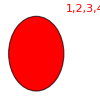
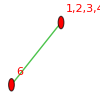
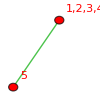
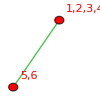
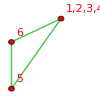
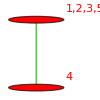
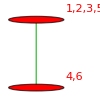
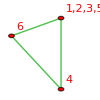
{-Graphics-{14348906→v1,1/6},-Graphics-{14289097→v2,1/2},-Graphics-{14169481→v3,1/2},-Graphics-{14109674→v4,1/2},-Graphics-{14109673→v5,1},-Graphics-{13810649→v6,1/2},-Graphics-{13750846→v7,1/2},-Graphics-{13750843→v8,1},-Graphics-{13631242→v9,1/2},-Graphics-{13631233→v10,1},-Graphics-{13571441→v11,1/2},-Graphics-{13571437→v12,1},-Graphics-{13571431→v13,1},-Graphics-{13571429→v14,1},-Graphics-{13571428→v15,1},-Graphics-{12734549→v16,1/2},-Graphics-{12674794→v17,1/2},-Graphics-{12674767→v18,1},-Graphics-{12555286→v19,1/2},-Graphics-{12555205→v20,1},-Graphics-{12495533→v21,1/2},-Graphics-{12495505→v22,1},-Graphics-{12495451→v23,1},-Graphics-{12495425→v24,1},-Graphics-{12495424→v25,1},-Graphics-{12196778→v26,1/2},-Graphics-{12196535→v27,1},-Graphics-{12137029→v28,1/2},-Graphics-{12136999→v29,1},-Graphics-{12136783→v30,1},-Graphics-{12136759→v31,1},-Graphics-{12136756→v32,1},-Graphics-{12017533→v33,1/2},-Graphics-{12017443→v34,1},-Graphics-{12017281→v35,1},-Graphics-{12017209→v36,1},-Graphics-{12017200→v37,1},-Graphics-{11957786→v38,1/2},-Graphics-{11957755→v39,1},-Graphics-{11957695→v40,1},-Graphics-{11957666→v41,1},-Graphics-{11957665→v42,1},-Graphics-{11957531→v43,1},-Graphics-{11957506→v44,1},-Graphics-{11957503→v45,1},-Graphics-{11957458→v46,1},-Graphics-{11957449→v47,1},-Graphics-{11957435→v48,1},-Graphics-{11957431→v49,1},-Graphics-{11957425→v50,1},-Graphics-{11957423→v51,1},-Graphics-{11957422→v52,0},-Graphics-{9536777→v53,1/2},-Graphics-{9478426→v54,1/2},-Graphics-{9477697→v55,1},-Graphics-{9361726→v56,1/2},-Graphics-{9359539→v57,1},-Graphics-{9303377→v58,1/2},-Graphics-{9302647→v59,1},-Graphics-{9301189→v60,1},-Graphics-{9300461→v61,1},-Graphics-{9300460→v62,1},-Graphics-{9011642→v63,1/2},-Graphics-{9005081→v64,1},-Graphics-{8953297→v65,1/2},-Graphics-{8952565→v66,1},-Graphics-{8946733→v67,1},-Graphics-{8946007→v68,1},-Graphics-{8946004→v69,1},-Graphics-{8836609→v70,1/2},-Graphics-{8834413→v71,1},-Graphics-{8830039→v72,1},-Graphics-{8827861→v73,1},-Graphics-{8827852→v74,1},-Graphics-{8778266→v75,1/2},-Graphics-{8777533→v76,1},-Graphics-{8776069→v77,1},-Graphics-{8775338→v78,1},-Graphics-{8775337→v79,1},-Graphics-{8771693→v80,1},-Graphics-{8770966→v81,1},-Graphics-{8770963→v82,1},-Graphics-{8769514→v83,1},-Graphics-{8769505→v84,1},-Graphics-{8768789→v85,1},-Graphics-{8768785→v86,1},-Graphics-{8768779→v87,1},-Graphics-{8768777→v88,1},-Graphics-{8768776→v89,0},-Graphics-{7961786→v90,1/2},-Graphics-{7942103→v91,1},-Graphics-{7903489→v92,1/2},-Graphics-{7902733→v93,1},-Graphics-{7883779→v94,1},-Graphics-{7883077→v95,1},-Graphics-{7883050→v96,1},-Graphics-{7786897→v97,1/2},-Graphics-{7784629→v98,1},-Graphics-{7767133→v99,1},-Graphics-{7765027→v100,1},-Graphics-{7764946→v101,1},-Graphics-{7728602→v102,1/2},-Graphics-{7727845→v103,1},-Graphics-{7726333→v104,1},-Graphics-{7725578→v105,1},-Graphics-{7725577→v106,1},-Graphics-{7708811→v107,1},-Graphics-{7708108→v108,1},-Graphics-{7708081→v109,1},-Graphics-{7706704→v110,1},-Graphics-{7706623→v111,1},-Graphics-{7706003→v112,1},-Graphics-{7705975→v113,1},-Graphics-{7705921→v114,1},-Graphics-{7705895→v115,1},-Graphics-{7705894→v116,0},-Graphics-{7437137→v117,1/2},-Graphics-{7430333→v118,1},-Graphics-{7417211→v119,1},-Graphics-{7410893→v120,1},-Graphics-{7410650→v121,1},-Graphics-{7378846→v122,1/2},-Graphics-{7378087→v123,1},-Graphics-{7372039→v124,1},-Graphics-{7371286→v125,1},-Graphics-{7371283→v126,1},-Graphics-{7358893→v127,1},-Graphics-{7358188→v128,1},-Graphics-{7358161→v129,1},-Graphics-{7352572→v130,1},-Graphics-{7352329→v131,1},-Graphics-{7351873→v132,1},-Graphics-{7351843→v133,1},-Graphics-{7351627→v134,1},-Graphics-{7351603→v135,1},-Graphics-{7351600→v136,0},-Graphics-{7262266→v137,1/2},-Graphics-{7259989→v138,1},-Graphics-{7255453→v139,1},-Graphics-{7253194→v140,1},-Graphics-{7253185→v141,1},-Graphics-{7242259→v142,1},-Graphics-{7240144→v143,1},-Graphics-{7240063→v144,1},-Graphics-{7235932→v145,1},-Graphics-{7235689→v146,1},-Graphics-{7233835→v147,1},-Graphics-{7233745→v148,1},-Graphics-{7233583→v149,1},-Graphics-{7233511→v150,1},-Graphics-{7233502→v151,0},-Graphics-{7203977→v152,1/2},-Graphics-{7203217→v153,1},-Graphics-{7201699→v154,1},-Graphics-{7200941→v155,1},-Graphics-{7200940→v156,1},-Graphics-{7197161→v157,1},-Graphics-{7196407→v158,1},-Graphics-{7196404→v159,1},-Graphics-{7194901→v160,1},-Graphics-{7194892→v161,1},-Graphics-{7194149→v162,1},-Graphics-{7194145→v163,1},-Graphics-{7194139→v164,1},-Graphics-{7194137→v165,1},-Graphics-{7194136→v166,0},-Graphics-{7183943→v167,1},-Graphics-{7183237→v168,1},-Graphics-{7183210→v169,1},-Graphics-{7181827→v170,1},-Graphics-{7181746→v171,1},-Graphics-{7181123→v172,1},-Graphics-{7181095→v173,1},-Graphics-{7181041→v174,1},-Graphics-{7181015→v175,1},-Graphics-{7181014→v176,0},-Graphics-{7177613→v177,1},-Graphics-{7177370→v178,1},-Graphics-{7176913→v179,1},-Graphics-{7176883→v180,1},-Graphics-{7176667→v181,1},-Graphics-{7176643→v182,1},-Graphics-{7176640→v183,0},-Graphics-{7175515→v184,1},-Graphics-{7175425→v185,1},-Graphics-{7175263→v186,1},-Graphics-{7175191→v187,1},-Graphics-{7175182→v188,0},-Graphics-{7174817→v189,1},-Graphics-{7174786→v190,1},-Graphics-{7174726→v191,1},-Graphics-{7174697→v192,1},-Graphics-{7174696→v193,0},-Graphics-{7174562→v194,1},-Graphics-{7174537→v195,1},-Graphics-{7174534→v196,0},-Graphics-{7174489→v197,1},-Graphics-{7174480→v198,0},-Graphics-{7174466→v199,1},-Graphics-{7174462→v200,0},-Graphics-{7174456→v201,0},-Graphics-{7174454→v202,0},-Graphics-{7174453→v203,0}}

```mathematica
Table[CosyPrint6[k],{k,baseKeys6}]
```

```mathematica
{-Graphics-{14348906->v1,1/6},-Graphics-{14289097->v2,1/2},-Graphics-{->v3,1/2},-Graphics-{14109674->v4,1/2},-Graphics-{14109673->v5,1},-Graphics-{13810649->v6,1/2},-Graphics-{13750846->v7,1/2},-Graphics-{13750843->v8,1},-Graphics-{13631242->v9,1/2},-Graphics-{13631233->v10,1},-Graphics-{13571441->v11,1/2},-Graphics-{13571437->v12,1},-Graphics-{13571431->v13,1},-Graphics-{13571429->v14,1},-Graphics-{13571428->v15,1},-Graphics-{12734549->v16,1/2},-Graphics-{12674794->v17,1/2},-Graphics-{12674767->v18,1},-Graphics-{12555286->v19,1/2},-Graphics-{12555205->v20,1},-Graphics-{12495533->v21,1/2},-Graphics-{12495505->v22,1},-Graphics-{12495451->v23,1},-Graphics-{12495425->v24,1},-Graphics-{12495424->v25,1},-Graphics-{12196778->v26,1/2},-Graphics-{12196535->v27,1},-Graphics-{12137029->v28,1/2},-Graphics-{12136999->v29,1},-Graphics-{12136783->v30,1},-Graphics-{12136759->v31,1},-Graphics-{12136756->v32,1},-Graphics-{12017533->v33,1/2},-Graphics-{12017443->v34,1},-Graphics-{12017281->v35,1},-Graphics-{12017209->v36,1},-Graphics-{12017200->v37,1},-Graphics-{11957786->v38,1/2},-Graphics-{11957755->v39,1},-Graphics-{11957695->v40,1},-Graphics-{11957666->v41,1},-Graphics-{11957665->v42,1},-Graphics-{11957531->v43,1},-Graphics-{11957506->v44,1},-Graphics-{11957503->v45,1},-Graphics-{11957458->v46,1},-Graphics-{11957449->v47,1},-Graphics-{11957435->v48,1},-Graphics-{11957431->v49,1},-Graphics-{11957425->v50,1},-Graphics-{11957423->v51,1},-Graphics-{11957422->v52,0},-Graphics-{9536777->v53,1/2},-Graphics-{9478426->v54,1/2},-Graphics-{9477697->v55,1},-Graphics-{9361726->v56,1/2},-Graphics-{9359539->v57,1},-Graphics-{9303377->v58,1/2},-Graphics-{9302647->v59,1},-Graphics-{9301189->v60,1},-Graphics-{9300461->v61,1},-Graphics-{9300460->v62,1},-Graphics-{9011642->v63,1/2},-Graphics-{9005081->v64,1},-Graphics-{8953297->v65,1/2},-Graphics-{8952565->v66,1},-Graphics-{8946733->v67,1},-Graphics-{8946007->v68,1},-Graphics-{8946004->v69,1},-Graphics-{8836609->v70,1/2},-Graphics-{8834413->v71,1},-Graphics-{8830039->v72,1},-Graphics-{8827861->v73,1},-Graphics-{8827852->v74,1},-Graphics-{8778266->v75,1/2},-Graphics-{8777533->v76,1},-Graphics-{8776069->v77,1},-Graphics-{8775338->v78,1},-Graphics-{8775337->v79,1},-Graphics-{8771693->v80,1},-Graphics-{8770966->v81,1},-Graphics-{8770963->v82,1},-Graphics-{8769514->v83,1},-Graphics-{8769505->v84,1},-Graphics-{8768789->v85,1},-Graphics-{8768785->v86,1},-Graphics-{8768779->v87,1},-Graphics-{8768777->v88,1},-Graphics-{8768776->v89,0},-Graphics-{7961786->v90,1/2},-Graphics-{7942103->v91,1},-Graphics-{7903489->v92,1/2},-Graphics-{7902733->v93,1},-Graphics-{7883779->v94,1},-Graphics-{7883077->v95,1},-Graphics-{7883050->v96,1},-Graphics-{7786897->v97,1/2},-Graphics-{7784629->v98,1},-Graphics-{7767133->v99,1},-Graphics-{7765027->v100,1},-Graphics-{7764946->v101,1},-Graphics-{7728602->v102,1/2},-Graphics-{7727845->v103,1},-Graphics-{7726333->v104,1},-Graphics-{7725578->v105,1},-Graphics-{7725577->v106,1},-Graphics-{7708811->v107,1},-Graphics-{7708108->v108,1},-Graphics-{7708081->v109,1},-Graphics-{7706704->v110,1},-Graphics-{7706623->v111,1},-Graphics-{7706003->v112,1},-Graphics-{7705975->v113,1},-Graphics-{7705921->v114,1},-Graphics-{7705895->v115,1},-Graphics-{7705894->v116,0},-Graphics-{7437137->v117,1/2},-Graphics-{7430333->v118,1},-Graphics-{7417211->v119,1},-Graphics-{7410893->v120,1},-Graphics-{7410650->v121,1},-Graphics-{7378846->v122,1/2},-Graphics-{7378087->v123,1},-Graphics-{7372039->v124,1},-Graphics-{7371286->v125,1},-Graphics-{7371283->v126,1},-Graphics-{7358893->v127,1},-Graphics-{7358188->v128,1},-Graphics-{7358161->v129,1},-Graphics-{7352572->v130,1},-Graphics-{7352329->v131,1},-Graphics-{7351873->v132,1},-Graphics-{7351843->v133,1},-Graphics-{7351627->v134,1},-Graphics-{7351603->v135,1},-Graphics-{7351600->v136,0},-Graphics-{7262266->v137,1/2},-Graphics-{7259989->v138,1},-Graphics-{7255453->v139,1},-Graphics-{7253194->v140,1},-Graphics-{7253185->v141,1},-Graphics-{7242259->v142,1},-Graphics-{7240144->v143,1},-Graphics-{7240063->v144,1},-Graphics-{7235932->v145,1},-Graphics-{7235689->v146,1},-Graphics-{7233835->v147,1},-Graphics-{7233745->v148,1},-Graphics-{7233583->v149,1},-Graphics-{7233511->v150,1},-Graphics-{7233502->v151,0},-Graphics-{7203977->v152,1/2},-Graphics-{7203217->v153,1},-Graphics-{7201699->v154,1},-Graphics-{7200941->v155,1},-Graphics-{7200940->v156,1},-Graphics-{7197161->v157,1},-Graphics-{7196407->v158,1},-Graphics-{7196404->v159,1},-Graphics-{7194901->v160,1},-Graphics-{7194892->v161,1},-Graphics-{7194149->v162,1},-Graphics-{7194145->v163,1},-Graphics-{7194139->v164,1},-Graphics-{7194137->v165,1},-Graphics-{7194136->v166,0},-Graphics-{7183943->v167,1},-Graphics-{7183237->v168,1},-Graphics-{7183210->v169,1},-Graphics-{7181827->v170,1},-Graphics-{7181746->v171,1},-Graphics-{7181123->v172,1},-Graphics-{7181095->v173,1},-Graphics-{7181041->v174,1},-Graphics-{7181015->v175,1},-Graphics-{7181014->v176,0},-Graphics-{7177613->v177,1},-Graphics-{7177370->v178,1},-Graphics-{7176913->v179,1},-Graphics-{7176883->v180,1},-Graphics-{7176667->v181,1},-Graphics-{7176643->v182,1},-Graphics-{7176640->v183,0},-Graphics-{7175515->v184,1},-Graphics-{7175425->v185,1},-Graphics-{7175263->v186,1},-Graphics-{7175191->v187,1},-Graphics-{7175182->v188,0},-Graphics-{7174817->v189,1},-Graphics-{7174786->v190,1},-Graphics-{7174726->v191,1},-Graphics-{7174697->v192,1},-Graphics-{7174696->v193,0},-Graphics-{7174562->v194,1},-Graphics-{7174537->v195,1},-Graphics-{7174534->v196,0},-Graphics-{7174489->v197,1},-Graphics-{7174480->v198,0},-Graphics-{7174466->v199,1},-Graphics-{7174462->v200,0},-Graphics-{7174456->v201,0},-Graphics-{7174454->v202,0},-Graphics-{7174453->v203,0}}
```

```mathematica
Interrupt[]
```

```mathematica
EmbedGraph[assoc_,key_]:=Block[{val=assoc[key], sets, reference={2,6,5,6,3}, g, sub},
sets=val["vertexsets"];
g=VertexDelete[ Graph[plantri[[10000]]],1];
g=EdgeDelete[ g,{2<->6,6<->5,5<->6,6<->3,3<->2}];
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}];

g
]
```

```mathematica
Monitor[
Table[{key,If[
PlanarGraphQ[EmbedGraph[withComp6,key]],
withComp6[key]["compwhy"]="Embedding is planar and follows IH";withComp6[key]["comp"]=Greater,
withComp6[key]["comp"]=GreaterEqual
]},{key,Keys[withComp6]}],
key];
```

Part::partw: Part 6 of {2, 6, 5, 6, 3} does not exist.

EdgeAdd::graph: A graph object is expected at position 1 in ….

Part::partw: Part 6 of {2, 6, 5, 6, 3} does not exist.

VertexContract::graph: A graph object is expected at position 1 in ….

Part::partw: Part 6 of {2, 6, 5, 6, 3} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

EdgeAdd::graph: A graph object is expected at position 1 in ….

General::stop: Further output of EdgeAdd :: graph will be suppressed during this calculation.

VertexContract::graph: A graph object is expected at position 1 in ….

General::stop: Further output of VertexContract :: graph will be suppressed during this calculation.

## We now replace some of the "b" variables with our greek letters

```mathematica
stubbornForm6=withComp6;
```

```mathematica
Keys[stubbornForm6[1]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,colortable,colofour,colortable2,comp,marked}

```mathematica
CosyPrintThree[key_]:=ColorTablePrint[key,stubbornForm6,"colofour","colortable2"]
```

```mathematica
Table [CosyPrintThree[k],{k,Take[Keys[stubbornForm6],-10]}]
```

{-Graphics-13990056v1+v3GreaterEqual
( | = | ≠
1<->2 | v1+v3 | 0
1<->3 | v1+v3 | 0
1<->4 | v1+v3 | 0
1<->5 | v1 | v3
1<->6 | v1+v3 | 0
2<->3 | v1+v3 | 0
2<->4 | v1+v3 | 0
2<->5 | v1 | v3
2<->6 | v1+v3 | 0
3<->4 | v1+v3 | 0
3<->5 | v1 | v3
3<->6 | v1+v3 | 0
4<->5 | v1 | v3
4<->6 | v1+v3 | 0
5<->6 | v1 | v3),-Graphics-14049864v3+v4+v5GreaterEqual
( | = | ≠
1<->2 | v3+v4+v5 | 0
1<->3 | v3+v4+v5 | 0
1<->4 | v3+v4+v5 | 0
1<->5 | 0 | v3+v4+v5
1<->6 | v3 | v4+v5
2<->3 | v3+v4+v5 | 0
2<->4 | v3+v4+v5 | 0
2<->5 | 0 | v3+v4+v5
2<->6 | v3 | v4+v5
3<->4 | v3+v4+v5 | 0
3<->5 | 0 | v3+v4+v5
3<->6 | v3 | v4+v5
4<->5 | 0 | v3+v4+v5
4<->6 | v3 | v4+v5
5<->6 | v4 | v3+v5),-Graphics-14049865v3+v5GreaterEqual
( | = | ≠
1<->2 | v3+v5 | 0
1<->3 | v3+v5 | 0
1<->4 | v3+v5 | 0
1<->5 | 0 | v3+v5
1<->6 | v3 | v5
2<->3 | v3+v5 | 0
2<->4 | v3+v5 | 0
2<->5 | 0 | v3+v5
2<->6 | v3 | v5
3<->4 | v3+v5 | 0
3<->5 | 0 | v3+v5
3<->6 | v3 | v5
4<->5 | 0 | v3+v5
4<->6 | v3 | v5
5<->6 | 0 | v3+v5),-Graphics-14109672v4+v5GreaterEqual
( | = | ≠
1<->2 | v4+v5 | 0
1<->3 | v4+v5 | 0
1<->4 | v4+v5 | 0
1<->5 | 0 | v4+v5
1<->6 | 0 | v4+v5
2<->3 | v4+v5 | 0
2<->4 | v4+v5 | 0
2<->5 | 0 | v4+v5
2<->6 | 0 | v4+v5
3<->4 | v4+v5 | 0
3<->5 | 0 | v4+v5
3<->6 | 0 | v4+v5
4<->5 | 0 | v4+v5
4<->6 | 0 | v4+v5
5<->6 | v4 | v5),-Graphics-14109673v5GreaterEqual
( | = | ≠
1<->2 | v5 | 0
1<->3 | v5 | 0
1<->4 | v5 | 0
1<->5 | 0 | v5
1<->6 | 0 | v5
2<->3 | v5 | 0
2<->4 | v5 | 0
2<->5 | 0 | v5
2<->6 | 0 | v5
3<->4 | v5 | 0
3<->5 | 0 | v5
3<->6 | 0 | v5
4<->5 | 0 | v5
4<->6 | 0 | v5
5<->6 | 0 | v5),-Graphics-14109674v4GreaterEqual
( | = | ≠
1<->2 | v4 | 0
1<->3 | v4 | 0
1<->4 | v4 | 0
1<->5 | 0 | v4
1<->6 | 0 | v4
2<->3 | v4 | 0
2<->4 | v4 | 0
2<->5 | 0 | v4
2<->6 | 0 | v4
3<->4 | v4 | 0
3<->5 | 0 | v4
3<->6 | 0 | v4
4<->5 | 0 | v4
4<->6 | 0 | v4
5<->6 | v4 | 0),-Graphics-14169481v3GreaterEqual
( | = | ≠
1<->2 | v3 | 0
1<->3 | v3 | 0
1<->4 | v3 | 0
1<->5 | 0 | v3
1<->6 | v3 | 0
2<->3 | v3 | 0
2<->4 | v3 | 0
2<->5 | 0 | v3
2<->6 | v3 | 0
3<->4 | v3 | 0
3<->5 | 0 | v3
3<->6 | v3 | 0
4<->5 | 0 | v3
4<->6 | v3 | 0
5<->6 | 0 | v3),-Graphics-14229288v1+v2GreaterEqual
( | = | ≠
1<->2 | v1+v2 | 0
1<->3 | v1+v2 | 0
1<->4 | v1+v2 | 0
1<->5 | v1+v2 | 0
1<->6 | v1 | v2
2<->3 | v1+v2 | 0
2<->4 | v1+v2 | 0
2<->5 | v1+v2 | 0
2<->6 | v1 | v2
3<->4 | v1+v2 | 0
3<->5 | v1+v2 | 0
3<->6 | v1 | v2
4<->5 | v1+v2 | 0
4<->6 | v1 | v2
5<->6 | v1 | v2),-Graphics-14289097v2GreaterEqual
( | = | ≠
1<->2 | v2 | 0
1<->3 | v2 | 0
1<->4 | v2 | 0
1<->5 | v2 | 0
1<->6 | 0 | v2
2<->3 | v2 | 0
2<->4 | v2 | 0
2<->5 | v2 | 0
2<->6 | 0 | v2
3<->4 | v2 | 0
3<->5 | v2 | 0
3<->6 | 0 | v2
4<->5 | v2 | 0
4<->6 | 0 | v2
5<->6 | 0 | v2),-Graphics-14348906v1GreaterEqual
( | = | ≠
1<->2 | v1 | 0
1<->3 | v1 | 0
1<->4 | v1 | 0
1<->5 | v1 | 0
1<->6 | v1 | 0
2<->3 | v1 | 0
2<->4 | v1 | 0
2<->5 | v1 | 0
2<->6 | v1 | 0
3<->4 | v1 | 0
3<->5 | v1 | 0
3<->6 | v1 | 0
4<->5 | v1 | 0
4<->6 | v1 | 0
5<->6 | v1 | 0)}

```mathematica
ineqsthree=Table[stubbornForm6[k]["comp"][stubbornForm6[k]["colofour"],0],{k,Keys[stubbornForm6]}]//Simplify;
```

$Aborted

```mathematica
Take[ineqsthree,5]
```

```mathematica
{v1+v10+v11+v12+v13+v16+v15+v2+v3+v6+v5+v6+v7+v8+v9>0,v10+v12+v13+v15+v2+v3+v5+v7+v8+v9>0,v1+v11+v16+v6+v6>0,v10+v12+v16+v15+v2+v6+v5+v6+v8+v9>0,v10+v12+v15+v2+v5+v8+v9>0}
```

```mathematica
{v1+v2+v6+v6+v5>0,v2+v6+v6>0,v1+v5>0,v2+v6+v5>0,v2+v6>0}
```

```mathematica
ineqsthree2=Simplify[Fold[And,ineqsthree]];Length[ineqsthree2]
```

$Aborted

```mathematica
graphicsthree=Map[stubbornForm6[#,"colofour"]->stubbornForm6[#,"graph"]&,Select[Keys[stubbornForm6],Length[ListofVars[stubbornForm6[#,"colofour"]]]==1&]];TableForm[graphicsthree]
```

```mathematica
graphicsthree2=Map[stubbornForm6[#,"colofour"]->stubbornForm6[#,"graph"]&,Keys[stubbornForm6]];
```

```mathematica
Table [ColorTablePrint[k,stubbornForm6,"colofour","colortable2",Map[#[[1]]->Graph[#[[2]],ImageSize->{60,60}]&,graphicsthree2]],{k,Keys[stubbornForm6]}]
```

```mathematica
ExpressionToTable2[ineqsthree2]
```

```mathematica
{{v1>0}, {v2>0}, {v3>0}, {v6>0}, {v5>0}, {v6>0}, {v7≥0}, {v8≥0}, {v9>0}, {v10>0}, {v11>0}, {v12>0}, {v13≥0}, {v16>0}, {v15≥0}, {v7+v8>0}, {v13+v7>0}, {v15+v8>0}, {v13+v15>0}}
```

```mathematica
Style[ExpressionToTable2[ineqsthree2]/.graphicsthree//StandardForm,Large,Bold,Blue]
```

```mathematica
{{-Graphics->0}, {-Graphics->0}, {-Graphics->0}, {-Graphics->0}, {-Graphics->0}, {-Graphics->0}, {-Graphics-≥0}, {-Graphics-≥0}, {-Graphics->0}, {-Graphics->0}, {-Graphics->0}, {-Graphics->0}, {-Graphics-≥0}, {-Graphics->0}, {-Graphics-≥0}, {-Graphics-+-Graphics->0}, {-Graphics-+-Graphics->0}, {-Graphics-+-Graphics->0}, {-Graphics-+-Graphics->0}}
```

```mathematica
Map[stubbornForm6[#,"graph"]->Style[StandardForm[stubbornForm6[#,"colofour"]/.graphicsthree],Large,Bold,Blue]&,Select[Keys[stubbornForm6],Length[ListofVars[stubbornForm6[#,"colofour"]]]!=1&]]//TableForm
```

```mathematica
{{-Graphics-->-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-}, {-Graphics-->-Graphics-+-Graphics-+-Graphics-}, {-Graphics-->-Graphics-+-Graphics-}, {-Graphics-->-Graphics-+-Graphics-+-Graphics-}, {-Graphics-->-Graphics-+-Graphics-}, {-Graphics-->-Graphics-+-Graphics-}, {-Graphics-->-Graphics-+-Graphics-+-Graphics-}, {-Graphics-->-Graphics-+-Graphics-}, {-Graphics-->-Graphics-+-Graphics-}, {-Graphics-->-Graphics-+-Graphics-}}
```